{{1,3.},{2,6.09},{3,11.37},{4,18.5},{5,27.55},{6,41.55},{7,56.86},{8,75.81},{9,97.33},{10,119.03}}

{{1,4.},{2,8.05},{3,16.12},{4,30.2},{5,52.48},{6,73.94},{7,119.18},{8,188.55},{9,273.74},{10,374.41}}

{{1,2.},{2,3.00899},{3,4.01078},{4,4.91648},{5,5.7137},{6,6.20828},{7,6.897},{8,7.5588},{9,8.09666},{10,8.54848}}

M2MA line

FittedModel[-25.432+12.9347 x]

0.936969

M2MA parabola

FittedModel[-0.224807 x+1.21245 x^2]

0.999616

Log DFA line

FittedModel[1.73837+0.719553 x]

0.984146

Fitted Equations

-0.224807 x+1.21245 x^2

1.73837+0.719553 x

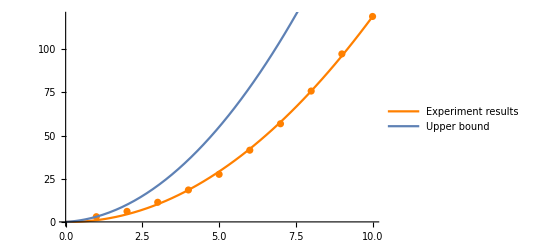

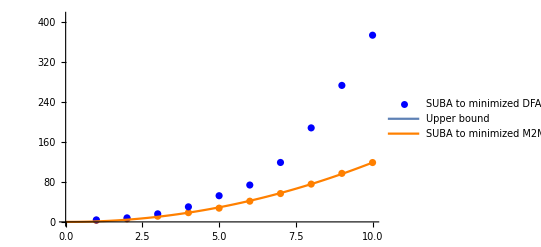

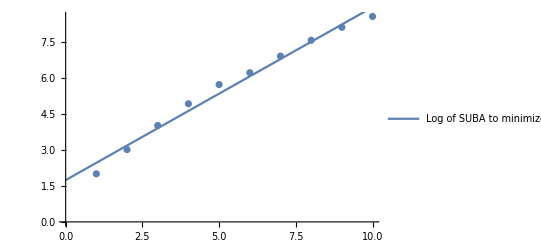

```mathematica
M2MAData = {{1, 3.00}, {2, 6.09}, {3, 11.37}, {4, 18.50}, {5, 27.55}, {6, 41.55}, {7, 56.86}, {8, 75.81}, {9, 97.33}, {10, 119.03}}

DFAData = {{1, 4.00}, {2, 8.05}, {3, 16.12}, {4, 30.20}, {5, 52.48}, {6, 73.94}, {7, 119.18}, {8, 188.55}, {9, 273.74}, {10, 374.41}}

LogDFAData = {{1, Log2[4.00]}, {2, Log2[8.05]}, {3, Log2[16.12]}, {4, Log2[30.20]}, {5, Log2[52.48]}, {6, Log2[73.94]}, {7, Log2[119.18]}, {8, Log2[188.55]}, {9, Log2[273.74]}, {10, Log2[374.41]}}

Print["M2MA line"]
M2MALineModel=LinearModelFit[M2MAData,x,x]
M2MALineModel["RSquared"]

Print["M2MA parabola"]
M2MAQuadraticModel=NonlinearModelFit[M2MAData,a*x^2+b*x,{a,b},x]
M2MAQuadraticModel["RSquared"]

Print["Log DFA line"]
LogDFALinearModel=LinearModelFit[LogDFAData,x,x]
LogDFALinearModel["RSquared"]

Print["Fitted Equations"]
M2MAParabola=Fit[M2MAData,{x, x^2},x]
LogDFALine = Fit[LogDFAData, {1, x}, x]

Show[ListPlot[M2MAData,PlotStyle->Orange],Plot[M2MAParabola,{x,0,10}, PlotStyle->Orange, PlotLegends->LineLegend[{"Experiment results"}]],Plot[2n^2+n, {n, 0, 10}, PlotLegends->LineLegend[{"Upper bound"}]],AxesLabel-> {"SUBA Size"}, ImageSize -> Scaled[.3]]

Show[ListPlot[M2MAData,PlotStyle->Orange],ListPlot[DFAData,PlotStyle->Blue, PlotLegends->LineLegend[{"SUBA to minimized DFA"}]],Plot[2^n+(2^n)*3^(n^2) , {n, 0, 10}, PlotLegends->LineLegend[{"Upper bound"}]],Plot[M2MAParabola,{x,0,10}, PlotStyle->Orange, PlotLegends->LineLegend[{"SUBA to minimized M2MA"}]],AxesLabel-> {"SUBA Size"}, ImageSize -> Scaled[.3], PlotRange->{{0, 10}, {0,412}}]

Show[ListPlot[LogDFAData],Plot[LogDFALine,{x,0,10}, PlotLegends->LineLegend[{"Log of SUBA to minimized DFA"}]], AxesLabel-> {"SUBA Size"}, ImageSize -> Scaled[.3]]
```